```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
Clear[partpath,impVoltages,impLatticesites,impCurrents,meanVoltages,sortedData,reallySortedData,currentData,sortedCurrentInput,sortedLatticeSites,data];
```

```mathematica
(*************************************************
Data that should work with this notebook:
Data\OBC_hermitian\current_stabilized\*any*

Mind the rght current input position.
************************************************)
```

```mathematica
Clear[partpath,impVoltages,impLatticesites,impCurrents];
(*partpath="D:\\GitHubDesktop\\eti\\Data\\OBC_hermitian\\Input unit cell 4,1,ALL 2Vpp";*)

(* partpath="C:\\Users\\Brand\\Desktop\\Promotion\\ETI\\ETI test data\\wtf\\Input unit cell 4,1,ALL 2Vpp";*)

NUnit=8;
MultiplexerSteps=32;
shunt=20.;
{x,y}={4,1};
Frequency = 2.2*10^6;
(************************* Mind the left out boards ************************************************)
Nvertical=8;
(*************************************************************************************************)
partpath="C:\\Users\\Nelson's Laptop\\Documents\\Git\\eti\\Data\\OBC_hermitian\\Input unit cell 4,4,ALL 2Vpp";
(*partpath ="C:\\Users\\Nelson's Laptop\\Documents\\Git\\eti\\Data\\000 Best Data yet\\obc\\8 vertical boards\\Input unit cell (4,1), _ MHz, 2 Vpp (21.09.28)";*)
(*partpath="D:\\GitHubDesktop\\eti\\Data\\OBC_hermitian\\Input unit cell 4,1,ALL 2Vpp";*)
standardizedUnitCellPositionDataSet=If[Nvertical==6,"C:\\Users\\Nelson's Laptop\\Documents\\Git\\eti\\Data\\OBC_hermitian\\standardizedUnitCellPositionDataSet\\NverticalEquals6\\","C:\\Users\\Nelson's Laptop\\Documents\\Git\\eti\\Data\\OBC_hermitian\\standardizedUnitCellPositionDataSet\\"];

impVoltages={};
impLatticesites={};
impCurrents={};

impVoltages=Import[partpath<>"\\2D_Measurement_01*.dat",HeaderLines->1];
impLatticesites=Import[standardizedUnitCellPositionDataSet<>"\\2D_Measurement_02*.dat",HeaderLines->1];
impCurrents=Import[partpath<>"\\Current\\2D_Measurement_01*.dat",HeaderLines->1];
```

```mathematica
(*
flattenedVoltage=ArrayReshape[impVoltages,{8*512,400,5}];
flattenedCurrents=ArrayReshape[impCurrents,{8*512,400,5}];
flattenedLatticesites=ArrayReshape[impLatticesites,{8*512,400,5}];
*)
```

```mathematica
meanVoltages=Map[Mean,Partition[#,100]&/@impVoltages,{2}];
```

```mathematica
singleLayerRaw=;
```

```mathematica
singleLayer[q_]:={#[[1]],#[[2]],q,#[[4]]}&/@singleLayerRaw;
allPositions=ArrayReshape[Table[Partition[#,4]&/@Table[singleLayer[q],{q,1,8}],{p,1,16}],{4096,4,4}];
```

```mathematica
(*sortedLatticeSites=(SortBy[#,#[[1]]]&/@impLatticesites); *)(*Voltage data sorted by increasing Lock-In number -> sort LatticeSites in the same way*)
data=Table[Flatten[{meanVoltages[[m,q,2]]+ⅈ meanVoltages[[m,q,3]],allPositions[[m,q]]}],{m,1,Dimensions[impVoltages][[1]]},{q,1,4}];
(*structure of original data: [[Measurements],[Lock-Ins],[Voltage,DimX1,DimX2,DimX3,Sublattice]]*)
```

```mathematica
(*
sortedData=Table[{},{i,1,(Dimensions[data][[1]])/(Nvertical*MultiplexerSteps)}];
(* sortedData: (Dimensions[data][[1]])/(Nvertical*MultiplexerSteps) leere Listen *)
Clear[j];
For[i=1,i<=Dimensions[data][[1]],i++,
j=If[QuotientRemainder[i,(Dimensions[data][[1]])/Nvertical][[2]]==0,(Dimensions[data][[1]])/Nvertical,QuotientRemainder[i,(Dimensions[data][[1]])/Nvertical][[2]]];
(* j läuft von 1 bis 512 *)
AppendTo[sortedData[[If[QuotientRemainder[j,MultiplexerSteps][[2]]==0,Quotient[j,MultiplexerSteps],Quotient[j,MultiplexerSteps]+1]]],data[[i]]];
]
*)
```

```mathematica
sortedData=ArrayReshape[data,{(Dimensions[data][[1]])/(Nvertical*MultiplexerSteps),(Dimensions[data][[1]])/(Nvertical/2),Dimensions[data][[3]]}];
```

```mathematica
(*

Structure reallySortedData: voltage, x1, x2, x3, sublattice site.
Sorted by current input (index i), then x3 component (#[[4]]), then sublattice site (#[[5]]) and then x1, x2 in ascending order.

*)

(*
reallySortedData=Table[Partition[SortBy[sortedData[[i]],(#[[5]]*10^3+#[[4]]*10^4+#[[3]]*10^2+#[[2]]*10)&],NUnit^2],{i,1,(Dimensions[data][[1]])/(Nvertical*MultiplexerSteps)}];
*)
part328=Partition[Partition[data,32],Nvertical];



reallySortedData=ArrayReshape[Table[If[OddQ[p],Partition[SortBy[Flatten[part328[[(p+1)/2,q]],1],#[[5]]*10^3+#[[4]]*10^2+#[[3]]*10^2+#[[2]]&],64],Partition[SortBy[Flatten[part328[[Nvertical+p/2,q]],1],#[[5]]*10^3+#[[4]]*10^2+#[[3]]*10^2+#[[2]]&],64]],{p,1,2*Nvertical},{q,1,Nvertical}],{2*Nvertical,2*Nvertical,NUnit^2,5}];
```

## Position of current input:

```mathematica
currentData=(#[[2]]+ⅈ #[[3]])/shunt&/@Flatten[Map[Mean,Partition[#,100]&/@impCurrents,{2}],1];
sortedCurrentInput=Table[{currentData[[w]]*KroneckerDelta[x+(y-1)*8,q]},{w,1,(Dimensions[data][[1]])/(Nvertical*MultiplexerSteps)},{q,1,NUnit^2}];
```

```mathematica
reallySortedData//Dimensions
reallySortedData[[3,1,1]]
```

{16,16,64,5}

{0.0027132+0.00114631 ⅈ,1.,1.,1,1.}

```mathematica
(*emptyVoltageMatrix = RandomReal[{0},{64*2*Nvertical,64*2*Nvertical}];
voltageVector[curr_,xshift_,yshift_]:= Flatten@Table[reallySortedData[[curr,i,If[Mod[pos,8,1]-Mod[pos+xshift,8,1]<1,Mod[pos+xshift+8*yshift,64,1],Mod[pos+xshift+8*yshift-8,64,1]],1]],{pos,1,64,1},{i,1,2*Nvertical,1}]
Do[emptyVoltageMatrix[[i+64*(z-1)]]=voltageVector[z,(reallySortedData[[1,1,i,2;;3]])[[1]],(reallySortedData[[1,1,i,2;;3]])[[1]]],{i,1,64,1},{z,1,2*Nvertical,1}];
currentVector = Flatten@Table[sortedCurrentInput[[i,;;,1]],{i,1,2*Nvertical,1}];
currentDiagMatrix = DiagonalMatrix@currentVector;
voltageMatrix = emptyVoltageMatrix;*)
```

```mathematica
(*OBCLapReal = Dot[currentDiagMatrix,Transpose@voltageMatrix];
OBCLapRealEigensystem = Eigensystem@OBCLapReal;*)
```

```mathematica
Clear[Vk,Ik,Greens]
(*VkTheo[i_,u_,kx_,ky_]:=∑_(l=1)^NUnitTheo ( ∑_(j=1)^NUnitTheo reallySortedDataTheo[[i,u,((l-1)*NUnitTheo)+j,1]]*Exp[-ⅈ*2*π*kx*j/NUnitTheo])*Exp[-ⅈ*2*π*ky*l/NUnitTheo];
IkTheo[i_,kx_,ky_]:=∑_(l=1)^NUnitTheo ( ∑_(j=1)^NUnitTheo sortedCurrentInputTheo[[i,((l-1)*NUnitTheo)+j,1]]*Exp[-ⅈ*2*π*kx*j/NUnitTheo])*Exp[-ⅈ*2*π*ky*l/NUnitTheo];*)
VkExp[i_,u_,kx_,ky_]:=∑_(l=1)^NUnit ( ∑_(j=1)^NUnit reallySortedData[[i,u,((l-1)*NUnit)+j,1]]*Exp[-ⅈ*2*π*kx*(j-1)/NUnit])*Exp[-ⅈ*2*π*ky*(l-1)/NUnit];
IkExp[i_,kx_,ky_]:=∑_(l=1)^NUnit ( ∑_(j=1)^NUnit sortedCurrentInput[[i,((l-1)*NUnit)+j,1]]*Exp[-ⅈ*2*π*kx*(j-1)/NUnit])*Exp[-ⅈ*2*π*ky*(l-1)/NUnit];
```

```mathematica
(*
GreensTheo[kx_,ky_]:=Table[VkTheo[w,v,kx,ky][[1]]/IkTheo[v,kx,ky],{v,1,16},{w,1,16}];
*)
GreensExp[kx_,ky_]:=Table[VkExp[w,v,kx,ky]/IkExp[v,kx,ky],{v,1,2*Nvertical},{w,1,2*Nvertical}];
```

```mathematica
VkExp[1,1,1,1]
GreensExp[1,1]//Dimensions
```

-1.67606+0.399401 ⅈ

{16,16}

```mathematica
Clear[n1];
SetSharedVariable[n1];
n1=0;
resultOBCExpComplex={};
Monitor[
resultOBCExpComplex=Parallelize[Table[
If[ky==1,n1++];
Eigensystem[GreensExp[kx-1,ky-1]]^-1,{kx,1,NUnit},{ky,1,NUnit}]];
,Row[{"Step 1/1 ",ProgressIndicator[n1,{1,NUnit^2}]}]];
```

```mathematica
resultOBCExpComplex//Dimensions
```

{8,8,2,16}

```mathematica
(*
Clear[n1];
SetSharedVariable[n1];
n1=0;
Monitor[
resultOBCTheoComplex=Parallelize[Table[
If[ky==1,n1++];
Eigensystem[GreensTheo[kx-1,ky-1]]^-1,{kx,1,NUnitTheo},{ky,1,NUnitTheo}]];
,Row[{"Step 1/1 ",ProgressIndicator[n1,{1,NUnitTheo^2}]}]];
*)
```

```mathematica
Frequency = 2.5*10^6;
Omega = 2*π*Frequency;
LBZ = 27*10^-6;
L0A=5.6*10^-6;
L0B = 27*10^-6;
initialC = 150*10^-12;
C1 = Omega*150*10^-12;
CAz = C1;
Cy = C1/2;
alpha = -Omega/(Omega^2*L0A);
beta = -Omega/(Omega^2*L0B);
betaZ =  -Omega/(Omega^2*LBZ);

NhorizontalTheory = 8;
NverticalTheoryZ = 8;

PathCoordXTheory = Join[Subdivide[0,0,Abs[2π-(3Pi)/2]*NhorizontalTheory/(2π)],
Subdivide[2Pi/NhorizontalTheory,Pi,Abs[π-(2Pi)/NhorizontalTheory]*NhorizontalTheory/(2π)],
Subdivide[Pi,Pi,Abs[(3Pi)/2+(2Pi)/NhorizontalTheory-2π]*NhorizontalTheory/(2π)+Abs[(2Pi)/NhorizontalTheory-π/2]*NhorizontalTheory/(2π)+1],
Subdivide[(2π)/2+2π/NhorizontalTheory,2Pi,Abs[(2π)/2+2π/NhorizontalTheory-2Pi]*NhorizontalTheory/(2π)],
Subdivide[2Pi,2Pi,Abs[π/2-(2π)/NhorizontalTheory]*NhorizontalTheory/(2π)]];

PathCoordYTheory = Join[Subdivide[2π,(3Pi)/2,Abs[2π-(3Pi)/2]*NhorizontalTheory/(2π)],
Subdivide[(3Pi)/2,(3Pi)/2,Abs[π-(2Pi)/NhorizontalTheory]*NhorizontalTheory/(2π)],
Subdivide[(3Pi)/2+(2Pi)/NhorizontalTheory,2π,Abs[(3Pi)/2+(2Pi)/NhorizontalTheory-2π]*NhorizontalTheory/(2π)],
Subdivide[2π/NhorizontalTheory,π/2,Abs[(2Pi)/NhorizontalTheory-π/2]*NhorizontalTheory/(2π)],
Subdivide[π/2,π/2,Abs[(2π)/2+2π/NhorizontalTheory-2Pi]*NhorizontalTheory/(2π)],
Subdivide[π/2-(2π)/NhorizontalTheory,0,Abs[π/2-(2π)/NhorizontalTheory]*NhorizontalTheory/(2π)]];

PathCoordX = Join[Subdivide[0,0,2],Subdivide[Pi/4,Pi,3],Subdivide[Pi,Pi,3],Subdivide[(5π)/4,2Pi,3],Subdivide[2Pi,2Pi,1]];
PathCoordY = Join[Subdivide[2π,(3Pi)/2,2],Subdivide[(3Pi)/2,(3Pi)/2,3],Subdivide[(7Pi)/4,2π,1],Subdivide[π/4,π/2,1],Subdivide[Pi/2,Pi/2,3],Subdivide[Pi/4,0,1]];


p1Theory = 1;
p2Theory = 1+Abs[2π-(3Pi)/2]*NhorizontalTheory/(2π);
p3Theory = 1+Abs[2π-(3Pi)/2]*NhorizontalTheory/(2π)+ Abs[π-(2Pi)/NhorizontalTheory]*NhorizontalTheory/(2π)+1;
p4Theory = 1+Abs[2π-(3Pi)/2]*NhorizontalTheory/(2π)+ Abs[π-(2Pi)/NhorizontalTheory]*NhorizontalTheory/(2π)+Abs[(3Pi)/2+(2Pi)/NhorizontalTheory-2π]*NhorizontalTheory/(2π)+Abs[(2Pi)/NhorizontalTheory-π/2]*NhorizontalTheory/(2π)+1+2;
p5Theory = 1+Abs[2π-(3Pi)/2]*NhorizontalTheory/(2π)+ Abs[π-(2Pi)/NhorizontalTheory]*NhorizontalTheory/(2π)+Abs[(3Pi)/2+(2Pi)/NhorizontalTheory-2π]*NhorizontalTheory/(2π)+Abs[(2Pi)/NhorizontalTheory-π/2]*NhorizontalTheory/(2π)+1+Abs[(2π)/2+2π/NhorizontalTheory-2Pi]*NhorizontalTheory/(2π)+3;
p6Theory = 1+Abs[2π-(3Pi)/2]*NhorizontalTheory/(2π)+ Abs[π-(2Pi)/NhorizontalTheory]*NhorizontalTheory/(2π)+Abs[(3Pi)/2+(2Pi)/NhorizontalTheory-2π]*NhorizontalTheory/(2π)+Abs[(2Pi)/NhorizontalTheory-π/2]*NhorizontalTheory/(2π)+1+Abs[(2π)/2+2π/NhorizontalTheory-2Pi]*NhorizontalTheory/(2π)+Abs[π/2-(2π)/NhorizontalTheory]*NhorizontalTheory/(2π)+4;
```

```mathematica
Xi={PauliMatrix[0],PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};
X[Mu_]:=Xi[[Mu+1]]

HcOBC[{kx_,ky_},z_]:=Sum[1/NverticalTheoryZ *(N[{{2CAz+2C1+2Cy,0},{0,2C1+2Cy+2betaZ}}-{{2CAz*Cos[ky],C1+C1*Exp[-I*kz]+2Cy*Cos[ky-kx]},{C1+C1*Exp[I*kz]+2Cy*Cos[ky-kx],2betaZ*Cos[ky]}}+{{alpha,0},{0,beta}}])*Exp[I*kz*z],{kz,0,(NverticalTheoryZ-1)2π/NverticalTheoryZ,2π/NverticalTheoryZ}]


HcOBCMatrix[kx_,ky_] :=ArrayFlatten[Table[Which[xpos == ypos,HcOBC[{kx,ky},0],xpos == ypos +1,HcOBC[{kx,ky},1],xpos == ypos-1,HcOBC[{kx,ky},-1],True,0],{xpos,1,NverticalTheoryZ},{ypos,1,NverticalTheoryZ}]];

HcOBCMatrixReal[x_,y_]:= Sum[1/(NUnit^2)*(HcOBCMatrix[kx,ky])*Exp[I*kx*x]*Exp[I*ky*y],{kx,0,(NUnit-1)2π/NUnit,2π/NUnit},{ky,0,(NUnit-1)2π/NUnit,2π/NUnit}]

scaling = 2;
HcIPR[state_]:=RGBColor[((Sum[Abs[state[[i]]]^4,{i,1,2*NverticalTheoryZ}])/(Sum[Abs[state[[i]]]^2,{i,1,2*NverticalTheoryZ}]))^scaling,0,0]

HcOBCSortedEigenstateContributionsColor[state_]:=Block[{normStateTheory = Normalize[state]},
RGBColor[(Norm[normStateTheory[[1;;2]]])^scaling,0,(Norm[normStateTheory[[2*NverticalTheoryZ-1;;2*NverticalTheoryZ]]])^scaling]];

HcOBCMatrixSortedEigensystem[kx_,ky_] := Block[{unsortedEigensystem=Eigensystem[HcOBCMatrix[kx,ky]]},unsortedEigensystem[[;;,Ordering[unsortedEigensystem[[1]]]]]];

HcOBCMatrixUnsortedEigensystem[kx_,ky_] := Eigensystem[HcOBCMatrix[kx,ky]];

experimentOBCMatrixUnsortedEigensystem[kx_,ky_] := Eigensystem[resultOBCExpComplex[[If[kx==2π,1,1+kx*NUnit/(2*π)],If[ky==2π,1,1+ky*NUnit/(2*π)]]]];

experimentOBCMatrixSortedEigensystem[kx_,ky_] := Block[{unsortedEigensystem=resultOBCExpComplex[[If[kx==2π,1,1+kx*NUnit/(2*π)],If[ky==2π,1,1+ky*NUnit/(2*π)]]]},unsortedEigensystem[[;;,Ordering[Im[unsortedEigensystem[[1]]]]]]];
```

```mathematica
HcOBC[{0,0},1]
```

{{-1.0842×10^-19+0. ⅈ,-0.00235619-2.1684×10^-19 ⅈ},{-2.1684×10^-19+0. ⅈ,0.+0. ⅈ}}

```mathematica
NUnitTheory = NUnit;
fermiArc1ks = Table[{kx,π/2},{kx,π,2π,(2π)/NUnitTheory}];
fermiArc2ks = Table[{kx,3π/2},{kx,0,π,(2π)/NUnitTheory}];

fermiArc1Int = Table[{If[kx==2π,1,kx*NUnit/(2π)+1],π/2*NUnit/(2π)+1},{kx,π,2π,(2π)/NUnit}];
fermiArc2Int = Table[{If[kx==2π,1,kx*NUnit/(2π)+1],3π/2*NUnit/(2π)+1},{kx,0,π,(2π)/NUnit}];

integers = Table[If[kx==2π,1,kx*NUnit/(2π)+1],{kx,0,2π,(2π)/NUnit}];
```

```mathematica
referenceEnergiesUpper = Table[{fermiArc1ks[[i,1]],fermiArc1ks[[i,2]],HcOBCMatrixUnsortedEigensystem[fermiArc1ks[[i,1]],fermiArc1ks[[i,2]]][[1,-4]]},{i,1,Length[fermiArc1ks]}];
referenceEnergiesLower = Table[{fermiArc1ks[[i,1]],fermiArc1ks[[i,2]],HcOBCMatrixUnsortedEigensystem[fermiArc1ks[[i,1]],fermiArc1ks[[i,2]]][[1,-3]]},{i,1,Length[fermiArc1ks]}];

surfaceEnergies = Table[{kx,ky,HcOBCMatrixUnsortedEigensystem[kx,ky][[1]]},{kx,0,2π,(2π)/NUnitTheory},{ky,0,2π,(2π)/NUnitTheory}];

fermiArcEnergies1Upper = Table[{fermiArc1ks[[i,1]],fermiArc1ks[[i,2]],HcOBCMatrixUnsortedEigensystem[fermiArc1ks[[i,1]],fermiArc1ks[[i,2]]][[1,-2]]},{i,1,Length[fermiArc1ks]}];
fermiArcEnergies1Lower= Table[{fermiArc1ks[[i,1]],fermiArc1ks[[i,2]],HcOBCMatrixUnsortedEigensystem[fermiArc1ks[[i,1]],fermiArc1ks[[i,2]]][[1,-1]]},{i,1,Length[fermiArc1ks]}];
```

```mathematica
surfaceEnergies1Upper = ParallelTable[{kx,ky,Max[HcOBCMatrixUnsortedEigensystem[kx,ky][[1,-2;;-1]]]},{kx,0,2π,(2π)/NUnitTheory},{ky,0,2π,(2π)/NUnitTheory}];
surfaceEnergies1Lower = ParallelTable[{kx,ky,Min[HcOBCMatrixUnsortedEigensystem[kx,ky][[1,-2;;-1]]]},{kx,0,2π,(2π)/NUnitTheory},{ky,0,2π,(2π)/NUnitTheory}];

surfaceEnergies2Upper = ParallelTable[{kx,ky,Max[HcOBCMatrixUnsortedEigensystem[kx,ky][[1,-4;;-3]]]},{kx,0,2π,(2π)/NUnitTheory},{ky,0,2π,(2π)/NUnitTheory}];
surfaceEnergies2Lower = ParallelTable[{kx,ky,Min[HcOBCMatrixUnsortedEigensystem[kx,ky][[1,-4;;-3]]]},{kx,0,2π,(2π)/NUnitTheory},{ky,0,2π,(2π)/NUnitTheory}];

surfaceEnergies3Upper = ParallelTable[{kx,ky,Max[HcOBCMatrixUnsortedEigensystem[kx,ky][[1,-6;;-5]]]},{kx,0,2π,(2π)/NUnitTheory},{ky,0,2π,(2π)/NUnitTheory}];
surfaceEnergies3Lower = ParallelTable[{kx,ky,Min[HcOBCMatrixUnsortedEigensystem[kx,ky][[1,-6;;-5]]]},{kx,0,2π,(2π)/NUnitTheory},{ky,0,2π,(2π)/NUnitTheory}];
surfaceEnergies4Upper = ParallelTable[{kx,ky,Max[HcOBCMatrixUnsortedEigensystem[kx,ky][[1,-8;;-7]]]},{kx,0,2π,(2π)/NUnitTheory},{ky,0,2π,(2π)/NUnitTheory}];
surfaceEnergies4Lower = ParallelTable[{kx,ky,Min[HcOBCMatrixUnsortedEigensystem[kx,ky][[1,-8;;-7]]]},{kx,0,2π,(2π)/NUnitTheory},{ky,0,2π,(2π)/NUnitTheory}];

surfaceEnergies5Upper = ParallelTable[{kx,ky,Max[HcOBCMatrixUnsortedEigensystem[kx,ky][[1,-10;;-9]]]},{kx,0,2π,(2π)/NUnitTheory},{ky,0,2π,(2π)/NUnitTheory}];
surfaceEnergies5Lower = ParallelTable[{kx,ky,Min[HcOBCMatrixUnsortedEigensystem[kx,ky][[1,-10;;-9]]]},{kx,0,2π,(2π)/NUnitTheory},{ky,0,2π,(2π)/NUnitTheory}];

surfaceEnergies6Upper = ParallelTable[{kx,ky,Max[HcOBCMatrixUnsortedEigensystem[kx,ky][[1,-12;;-11]]]},{kx,0,2π,(2π)/NUnitTheory},{ky,0,2π,(2π)/NUnitTheory}];
surfaceEnergies6Lower = ParallelTable[{kx,ky,Min[HcOBCMatrixUnsortedEigensystem[kx,ky][[1,-12;;-11]]]},{kx,0,2π,(2π)/NUnitTheory},{ky,0,2π,(2π)/NUnitTheory}];
```

```mathematica
expSurfaceEnergies1Upper = ParallelTable[{kx,ky,Max[Im[resultOBCExpComplex[[If[kx==2π,1,kx*NUnit/(2π)+1],If[ky==2π,1,ky*NUnit/(2π)+1]]][[1,{1,-1}]]]]},{kx,0,2π,(2π)/NUnit},{ky,0,2π,(2π)/NUnit}];
expSurfaceEnergies1Lower = ParallelTable[{kx,ky,Min[Im[resultOBCExpComplex[[If[kx==2π,1,kx*NUnit/(2π)+1],If[ky==2π,1,ky*NUnit/(2π)+1]]][[1,{1,-1}]]]]},{kx,0,2π,(2π)/NUnit},{ky,0,2π,(2π)/NUnit}];

expSurfaceEnergies2Upper = ParallelTable[{kx,ky,Max[Im[resultOBCExpComplex[[If[kx==2π,1,kx*NUnit/(2π)+1],If[ky==2π,1,ky*NUnit/(2π)+1]]][[1,{2,-2}]]]]},{kx,0,2π,(2π)/NUnit},{ky,0,2π,(2π)/NUnit}];
expSurfaceEnergies2Lower = ParallelTable[{kx,ky,Min[Im[resultOBCExpComplex[[If[kx==2π,1,kx*NUnit/(2π)+1],If[ky==2π,1,ky*NUnit/(2π)+1]]][[1,{2,-2}]]]]},{kx,0,2π,(2π)/NUnit},{ky,0,2π,(2π)/NUnit}];

expSurfaceEnergies3Upper = ParallelTable[{kx,ky,Max[Im[resultOBCExpComplex[[If[kx==2π,1,kx*NUnit/(2π)+1],If[ky==2π,1,ky*NUnit/(2π)+1]]][[1,{3,-3}]]]]},{kx,0,2π,(2π)/NUnit},{ky,0,2π,(2π)/NUnit}];
expSurfaceEnergies3Lower = ParallelTable[{kx,ky,Min[Im[resultOBCExpComplex[[If[kx==2π,1,kx*NUnit/(2π)+1],If[ky==2π,1,ky*NUnit/(2π)+1]]][[1,{3,-3}]]]]},{kx,0,2π,(2π)/NUnit},{ky,0,2π,(2π)/NUnit}];
```

```mathematica
threshold = 0.9;
thresholdExp = 0.8;
middleInt = Round[NverticalTheoryZ/2];
NUnitTheory = NUnit;
NverticalTheoryZ = Nvertical;
width = 1;
bands = Table[NverticalTheoryZ+i,{i,-width,width+1,1}];
```

```mathematica
localization[state_,component_]:=Block[{normState = Normalize[state]},(Abs[normState[[component]]])]

localizedTable = Table[If[localization[HcOBCMatrixSortedEigensystem[kx,ky][[2,i]],j]>threshold,{kx,ky,HcOBCMatrixSortedEigensystem[kx,ky][[1,i]]},{kx,ky,10}],{kx,0,(NUnitTheory-1)2π/NUnitTheory,2π/NUnitTheory},{ky,0,(NUnitTheory-1)2π/NUnitTheory,2π/NUnitTheory},{i,bands},{j,1,2*NverticalTheoryZ}];

flatLozalizedTable = Flatten[localizedTable,{{1,2,3,4}}];
```

```mathematica
localizedTableExp = Table[If[localization[resultOBCExpComplex[[If[kx==2π,1,1+kx*NUnit/(2*π)],If[ky==2π,1,1+ky*NUnit/(2*π)]]][[2,i]],j]>thresholdExp,{kx,ky,Im[resultOBCExpComplex[[If[kx==2π,1,1+kx*NUnit/(2*π)],If[ky==2π,1,1+ky*NUnit/(2*π)]]][[1,i]]]},{kx,ky,10}],{kx,0,(NUnit-1)2π/NUnit,2π/NUnit},{ky,0,(NUnit-1)2π/NUnit,2π/NUnit},{i,bands},{j,1,2*Nvertical}];

flatLozalizedTableExp = Flatten[localizedTableExp,{{1,2,3,4}}];
```

```mathematica
upperBand = Flatten[Table[{kx,ky,HcOBCMatrixSortedEigensystem[kx,ky][[1,bands[[-1]]]]},{kx,0,(NUnitTheory-1)2π/NUnitTheory,2π/NUnitTheory},{ky,0,(NUnitTheory-1)2π/NUnitTheory,2π/NUnitTheory}],{{1,2}}];
lowerBand = Flatten[Table[{kx,ky,HcOBCMatrixSortedEigensystem[kx,ky][[1,bands[[1]]]]},{kx,0,(NUnitTheory-1)2π/NUnitTheory,2π/NUnitTheory},{ky,0,(NUnitTheory-1)2π/NUnitTheory,2π/NUnitTheory}],{{1,2}}];
```

```mathematica
upperBandExp = Flatten[Table[{kx,ky,Im[resultOBCExpComplex[[If[kx==2π,1,1+kx*NUnit/(2*π)],If[ky==2π,1,1+ky*NUnit/(2*π)]]][[1,bands[[-1]]]]]},{kx,0,(NUnit-1)2π/NUnit,2π/NUnit},{ky,0,(NUnit-1)2π/NUnit,2π/NUnit}],{{1,2}}];

lowerBandExp = Flatten[Table[{kx,ky,Im[resultOBCExpComplex[[If[kx==2π,1,1+kx*NUnit/(2*π)],If[ky==2π,1,1+ky*NUnit/(2*π)]]][[1,bands[[1]]]]]},{kx,0,(NUnit-1)2π/NUnit,2π/NUnit},{ky,0,(NUnit-1)2π/NUnit,2π/NUnit}],{{1,2}}];
```

```mathematica
HcOBCSortedPathEigensystem = ParallelTable[HcOBCMatrixSortedEigensystem[PathCoordXTheory[[i]],PathCoordYTheory[[i]]],{i,1,Length[PathCoordXTheory]}];

HcPathTheory =ParallelTable[{i,4*Re@HcOBCSortedPathEigensystem[[i,1,j]]},{i,1,Length[PathCoordXTheory]},{j,1,2*NverticalTheoryZ}];

HcPoints = ParallelTable[{HcOBCSortedEigenstateContributionsColor[HcOBCSortedPathEigensystem[[i,2,j]]],Point[{i,4*Re@HcOBCSortedPathEigensystem[[i,1,j]]}]},{i,1,Length[PathCoordXTheory]},{j,1,2*NverticalTheoryZ}];
```

```mathematica
res = 10;
sub = {"A","B"};
ticksReal = {{1,"(1,A)"},{2,"(1,B)"},{3,"(2,A)"},{4,"(2,B)"},{5,"(3,A)"},{6,"(3,B)"},{7,"(4,A)"},{8,"(4,B)"},{9,"(5,A)"},{10,"(5,B)"},{11,"(6,A)"},{12,"(6,B)"}};

subLocalizationMatrixTop1 =Re@Table[{i+1+res,(Norm[HcOBCMatrixUnsortedEigensystem[2π/4+i*π/(2*res),6π/4][[2,11]][[1;;6]][[1;;;;2]]]+Norm[HcOBCMatrixUnsortedEigensystem[2π/4+i*π/(2*res),6π/4][[2,12]][[1;;6]][[1;;;;2]]]-Norm[HcOBCMatrixUnsortedEigensystem[2π/4+i*π/(2*res),6π/4][[2,11]][[1;;6]][[2;;;;2]]]-Norm[HcOBCMatrixUnsortedEigensystem[2π/4+i*π/(2*res),6π/4][[2,12]][[1;;6]][[2;;;;2]]])/(Norm[HcOBCMatrixUnsortedEigensystem[2π/4+i*π/(2*res),6π/4][[2,11]][[1;;6]][[1;;;;2]]]+Norm[HcOBCMatrixUnsortedEigensystem[2π/4+i*π/(2*res),6π/4][[2,12]][[1;;6]][[1;;;;2]]]+Norm[HcOBCMatrixUnsortedEigensystem[2π/4+i*π/(2*res),6π/4][[2,11]][[1;;6]][[2;;;;2]]]+Norm[HcOBCMatrixUnsortedEigensystem[2π/4+i*π/(2*res),6π/4][[2,12]][[1;;6]][[2;;;;2]]])},{i,-res,res,1}];

subLocalizationMatrixTop2 = Re@Table[{i+1+res,(Norm[HcOBCMatrixUnsortedEigensystem[6π/4+i*π/(2*res),2π/4][[2,11]][[1;;6]][[1;;;;2]]]+Norm[HcOBCMatrixUnsortedEigensystem[6π/4+i*π/(2*res),2π/4][[2,12]][[1;;6]][[1;;;;2]]]-Norm[HcOBCMatrixUnsortedEigensystem[6π/4+i*π/(2*res),2π/4][[2,11]][[1;;6]][[2;;;;2]]]-Norm[HcOBCMatrixUnsortedEigensystem[6π/4+i*π/(2*res),2π/4][[2,12]][[1;;6]][[2;;;;2]]])/(Norm[HcOBCMatrixUnsortedEigensystem[6π/4+i*π/(2*res),2π/4][[2,11]][[1;;6]][[1;;;;2]]]+Norm[HcOBCMatrixUnsortedEigensystem[6π/4+i*π/(2*res),2π/4][[2,12]][[1;;6]][[1;;;;2]]]+Norm[HcOBCMatrixUnsortedEigensystem[6π/4+i*π/(2*res),2π/4][[2,11]][[1;;6]][[2;;;;2]]]+Norm[HcOBCMatrixUnsortedEigensystem[6π/4+i*π/(2*res),2π/4][[2,12]][[1;;6]][[2;;;;2]]])},{i,-res,res,1}];

subLocalizationMatrixBottom1 =Re@Table[{i+1+res,(Norm[HcOBCMatrixUnsortedEigensystem[2π/4+i*π/(2*res),6π/4][[2,11]][[7;;12]][[1;;;;2]]]+Norm[HcOBCMatrixUnsortedEigensystem[2π/4+i*π/(2*res),6π/4][[2,12]][[7;;12]][[1;;;;2]]]-Norm[HcOBCMatrixUnsortedEigensystem[2π/4+i*π/(2*res),6π/4][[2,11]][[7;;12]][[2;;;;2]]]-Norm[HcOBCMatrixUnsortedEigensystem[2π/4+i*π/(2*res),6π/4][[2,12]][[7;;12]][[2;;;;2]]])/(Norm[HcOBCMatrixUnsortedEigensystem[2π/4+i*π/(2*res),6π/4][[2,11]][[7;;12]][[1;;;;2]]]+Norm[HcOBCMatrixUnsortedEigensystem[2π/4+i*π/(2*res),6π/4][[2,12]][[7;;12]][[1;;;;2]]]+Norm[HcOBCMatrixUnsortedEigensystem[2π/4+i*π/(2*res),6π/4][[2,11]][[7;;12]][[2;;;;2]]]+Norm[HcOBCMatrixUnsortedEigensystem[2π/4+i*π/(2*res),6π/4][[2,12]][[7;;12]][[2;;;;2]]])},{i,-res,res,1}];

subLocalizationMatrixBottom2 = Re@Table[{i+1+res,(Norm[HcOBCMatrixUnsortedEigensystem[6π/4+i*π/(2*res),2π/4][[2,11]][[7;;12]][[1;;;;2]]]+Norm[HcOBCMatrixUnsortedEigensystem[6π/4+i*π/(2*res),2π/4][[2,12]][[7;;12]][[1;;;;2]]]-Norm[HcOBCMatrixUnsortedEigensystem[6π/4+i*π/(2*res),2π/4][[2,11]][[7;;12]][[2;;;;2]]]-Norm[HcOBCMatrixUnsortedEigensystem[6π/4+i*π/(2*res),2π/4][[2,12]][[7;;12]][[2;;;;2]]])/(Norm[HcOBCMatrixUnsortedEigensystem[6π/4+i*π/(2*res),2π/4][[2,11]][[7;;12]][[1;;;;2]]]+Norm[HcOBCMatrixUnsortedEigensystem[6π/4+i*π/(2*res),2π/4][[2,12]][[7;;12]][[1;;;;2]]]+Norm[HcOBCMatrixUnsortedEigensystem[6π/4+i*π/(2*res),2π/4][[2,11]][[7;;12]][[2;;;;2]]]+Norm[HcOBCMatrixUnsortedEigensystem[6π/4+i*π/(2*res),2π/4][[2,12]][[7;;12]][[2;;;;2]]])},{i,-res,res,1}];

subLocalizationMatrix = Join[subLocalizationMatrixTop1,subLocalizationMatrixTop2];
HcOBCMatrixUnsortedEigensystem[π/2-0*π/4,6π/4][[2,12]][[1;;6]][[1;;;;2]]//MatrixForm;
```

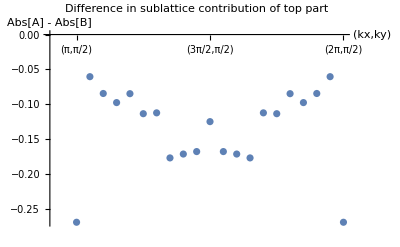

```mathematica
ListPlot[subLocalizationMatrixBottom2,PlotLabel->"Difference in sublattice contribution of top part",AxesLabel->{"(kx,ky)",ToString[Abs[A]-Abs[B]]},PlotRange->All,Ticks->{{{1,"(π,π/2)"},{res+1,"(3π/2,π/2)"},{2res+1,"(2π,π/2)"}},Automatic},AxesOrigin->{-1,0},PlotLegends->Automatic]
```

```mathematica
(*------------------------------------------*)
```

```mathematica
(*------------------------------------*)
```

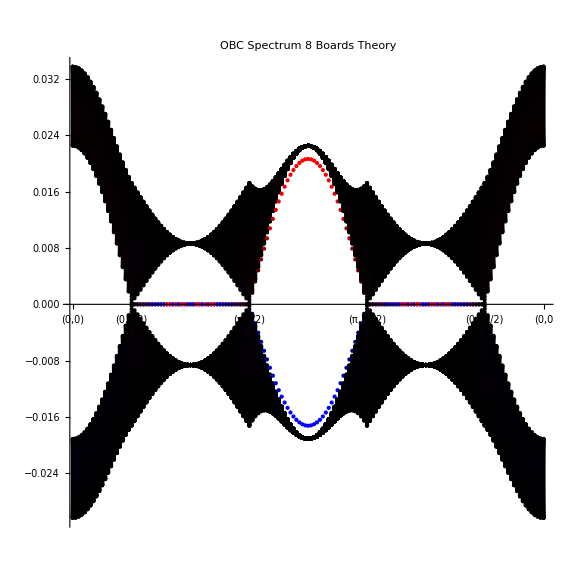

-Graphics-

```mathematica
sortedZBands[kx_,ky_]:=SortBy[Flatten[HcOBC[{kx,ky}][[;;,1,;;]]],Im[#]&]
BandsPathValuesTheory = Im@Transpose@Table[sortedZBands[PathCoordX[[i]],PathCoordY[[i]]],{i,1,Length[PathCoordX]}];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

```mathematica
kListExp=Table[(k-1)*(2π/NUnit),{k,1,NUnit+1}];
(*kListTheo=Table[(k-1)*(2π/NUnitTheo),{k,1,NUnitTheo+1}];*)
resultOBCExpImSorted=Table[Im[SortBy[resultOBCExpComplex[[a,b,1]],Im[#]&]],{a,1,NUnit},{b,1,NUnit}];
(*resultOBCTheoImSorted=Table[Im[SortBy[resultOBCTheoComplex[[a,b,1]],Im[#]&]],{a,1,NUnitTheo},{b,1,NUnitTheo}];*)
resultOBCExpImSortedEigensystem[kx_,ky_]:=SortBy[Transpose[resultOBCExpComplex[[If[kx==2π,1,1+kx*NUnit/(2π)],If[ky==2π,1,1+ky*NUnit/(2π)]]]],Im[#]&];
```

```mathematica
Table[{kListExp[[a]],resultOBCExpImSorted[[If[a==9,1,a],If[x==9,1,x],b]]},{a,1,9},{b,1,2*Nvertical}];
```

```mathematica
Manipulate[Labeled[ListPlot[Transpose@Table[{kListExp[[a]],resultOBCExpImSorted[[If[a==9,1,a],If[x==9,1,x],b]]},{a,1,9},{b,1,2*Nvertical}],Ticks->{{0,π/2,π,3π/2,2π},Automatic},PlotRange->{{-0.2,6.5},{-0.05,0.05}},ImageSize->Large,Joined->True,PlotLabel->"6 Board Measurement,   "<>"ky = "<>ToString[((x-1.)/8.)*2.]<>" × π"],{"kx","j_n"},{Bottom,Left},RotateLabel->True],{x,1,9,1}]
```

Part::partd: Part specification kListExp⟦1⟧ is longer than depth of object.

Part::partd: Part specification resultOBCExpImSorted⟦1,1,1⟧ is longer than depth of object.

Part::partd: Part specification kListExp⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {b,1,2 Nvertical} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Part::pkspec1: The expression a cannot be used as a part specification.

ListPlot::lpn: Transpose[Table[{kListExp⟦a⟧,resultOBCExpImSorted⟦If[a==9,1,a],If[FE`x$$5==9,1,FE`x$$5],b⟧},{a,1.,9.},{b,1.,2. Nvertical}]] is not a list of numbers or pairs of numbers.

Part::pkspec1: The expression a cannot be used as a part specification.

ListPlot::lpn: Transpose[Table[{kListExp⟦a⟧,resultOBCExpImSorted⟦If[a==9,1,a],If[FE`x$$5==9,1,FE`x$$5],b⟧},{a,1.,9.},{b,1.,2. Nvertical}]] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

```mathematica
BandsPathValues = Transpose@Table[resultOBCExpImSorted[[If[1+PathCoordX[[i]]4/π==9,1,1+PathCoordX[[i]]4/π],If[1+PathCoordY[[i]]4/π==9,1,1+PathCoordY[[i]]4/π]]],{i,1,Length[PathCoordX]}];
```

```mathematica
HcOBCSortedEigenstateContributionsColorExp[kx_,ky_]:=Flatten@Table[RGBColor[Norm[ (resultOBCExpImSortedEigensystem[kx,ky][[i,2]])[[Nvertical-1;;Nvertical]]]/Norm[(resultOBCExpImSortedEigensystem[kx,ky][[i,2]])],0,Norm[(resultOBCExpImSortedEigensystem[kx,ky][[i,2]])[[Nvertical+1;;Nvertical+2]]]/Norm[(resultOBCExpImSortedEigensystem[kx,ky][[i,2]])]],{i,1,Length[resultOBCExpImSortedEigensystem[kx,ky][[;;,1]]],1}]

HcOBCSortedEigenstateContributionsColorLowerExp[kx_,ky_]:=Flatten@Table[Norm[(resultOBCExpImSortedEigensystem[kx,ky][[i,2]])[[Nvertical+1;;Nvertical+2]]]/Norm[(resultOBCExpImSortedEigensystem[kx,ky][[i,2]])],{i,1,Length[resultOBCExpImSortedEigensystem[kx,ky][[;;,1]]],1}]

HcOBCSortedPathEigenstateContributionsColorsExp=Transpose[ParallelTable[HcOBCSortedEigenstateContributionsColorExp[PathCoordX[[i]],PathCoordY[[i]]],{i,1,Length[PathCoordX]}]];
```

```mathematica
expscaling = scaling;
ExperimentIPR[state_]:=Block[{normState=Normalize[state]},
RGBColor[((Sum[Abs[normState[[i]]]^4,{i,1,2*Nvertical}])/(Sum[Abs[normState[[i]]]^2,{i,1,2*Nvertical}]))^expscaling,0,0]]

(*experimentOBCSortedEigenstateContributionsColor[state_]:=RGBColor[((Norm[ state[[2*Nvertical-1;;2*Nvertical]]])/(Norm[ state]))^expscaling,0,((Norm[state[[1;;2]]])/(Norm[state]))^expscaling];*)

experimentOBCMatrixSortedEigensystem[kx_,ky_] := Block[{unsortedEigensystem=resultOBCExpComplex[[If[kx==2π,1,1+kx*NUnit/(2*π)],If[ky==2π,1,1+ky*NUnit/(2*π)]]]},unsortedEigensystem[[;;,Ordering[Im[unsortedEigensystem[[1]]]]]]];
```

```mathematica
experimentOBCSortedPathEigensystem = ParallelTable[experimentOBCMatrixSortedEigensystem[PathCoordX[[i]],PathCoordY[[i]]],{i,1,Length[PathCoordX]}];

experimentPath =ParallelTable[{i,Im@experimentOBCSortedPathEigensystem[[i,1,j]]},{i,1,Length[PathCoordX]},{j,1,2*Nvertical}];

ExperimentOBCSortedEigenstateContributionsColor[state_]:=Block[{normStateExperiment = Normalize[state]},
RGBColor[((Norm[ normStateExperiment[[1;;2]]]))^expscaling,0,((Norm[ normStateExperiment[[2*Nvertical-1;;2*Nvertical]]]))^expscaling]];

experimentPoints = ParallelTable[{ExperimentOBCSortedEigenstateContributionsColor[experimentOBCSortedPathEigensystem[[i,2,j]]],Point[{i,Im@experimentOBCSortedPathEigensystem[[i,1,j]]}]},{i,1,Length[PathCoordX]},{j,1,2*Nvertical}];

experimentMatrixform = Reverse[Transpose[experimentPoints][[;;,;;,1]]];
theoryMatrixform = Reverse[Transpose[HcPoints][[;;,;;,1]]];
```

```mathematica
Manipulate[ListPlot[Abs[experimentOBCMatrixSortedEigensystem[Pi/2,-Pi/2][[2,i]]],PlotRange->All],{i,1,12,1}];
```

```mathematica
Manipulate[ListPlot[Abs[resultOBCExpComplex[[a,b,2]]],PlotRange->All,ImageSize->Large,PlotStyle->Table[ColorData["Rainbow"][i/16],{i,1,16}],Joined->True],{a,1,8,1},{b,1,8,1}];
```

```mathematica
(*Manipulate[ListLogPlot[Abs[resultOBCTheoComplex[[a,b,2]]],PlotRange->All,ImageSize->Large],{a,1,24,1},{b,1,24,1}]*)
```

```mathematica
(*Manipulate[ComplexListPlot[resultOBCTheoComplex[[a,b,2]],PlotRange->All,ImageSize->Large],{a,1,24,1},{b,1,24,1}]*)
Manipulate[ComplexListPlot[resultOBCExpComplex[[a,b,2]],PlotRange->All,ImageSize->Large],{a,1,8,1},{b,1,8,1}];
```

```mathematica
(*Manipulate[ListPlot[Transpose@Table[{kListTheo[[a]],resultOBCTheoImSorted[[If[a==25,1,a],If[x==25,1,x],b]]},{a,1,25},{b,1,16}],Ticks->{{0,π/2,π,3π/2,2π},Automatic},PlotRange->{{-0.2,6.5},All},ImageSize->Large,Joined->True],{x,1,24,1}]*)
```

```mathematica
(*Manipulate[Show[ListPlot[Transpose@Table[{kListTheo[[a]],resultOBCTheoImSorted[[If[a==25,1,a],If[xx==25,1,xx],b]]},{a,1,25},{b,1,16}],Ticks->{{0,π/2,π,3π/2,2π},Automatic},PlotRange->{{-0.2,6.5},All},ImageSize->Large,Joined->True],ListPlot[Transpose@Table[{kListExp[[a]],Im[resultOBCExpComplex[[If[a==9,1,a],If[x==9,1,x],b]]]},{a,1,9},{b,1,16}],Ticks->{{0,π/2,π,3π/2,2π},Automatic},PlotRange->{{-0.2,6.5},All},ImageSize->Large],PlotRange->{{-0.2,6.5},All}],{x,1,9,1},{xx,1,25,1}]*)
```

Evaluation: High Symmetry Plot and IPR Localization

```mathematica
Omega=2 π Frequency;
LBZ=27/10^6;
L0A=5.6/10^6;
L0B=27/10^6;
initialC=150/10^12;
C1=(Omega 150)/10^12;
CAz=C1;
Cy=C1/2;
alpha=-Omega/(Omega^2 L0A);
beta=-Omega/(Omega^2 L0B);
betaZ=-Omega/(Omega^2 LBZ);
NhorizontalTheory=NUnit;
NverticalTheoryZ=Nvertical;
PathCoordXTheory=Join[Subdivide[0,0,(Abs[2 π-(3 π)/2] NhorizontalTheory)/(2 π)],Subdivide[(2 π)/NhorizontalTheory,π,(Abs[π-(2 π)/NhorizontalTheory] NhorizontalTheory)/(2 π)],Subdivide[π,π,(Abs[(3 π)/2+(2 π)/NhorizontalTheory-2 π] NhorizontalTheory)/(2 π)+(Abs[(2 π)/NhorizontalTheory-π/2] NhorizontalTheory)/(2 π)+1],Subdivide[(2 π)/2+(2 π)/NhorizontalTheory,2 π,(Abs[(2 π)/2+(2 π)/NhorizontalTheory-2 π] NhorizontalTheory)/(2 π)],Subdivide[2 π,2 π,(Abs[π/2-(2 π)/NhorizontalTheory] NhorizontalTheory)/(2 π)]];
PathCoordYTheory=Join[Subdivide[2 π,(3 π)/2,(Abs[2 π-(3 π)/2] NhorizontalTheory)/(2 π)],Subdivide[(3 π)/2,(3 π)/2,(Abs[π-(2 π)/NhorizontalTheory] NhorizontalTheory)/(2 π)],Subdivide[(3 π)/2+(2 π)/NhorizontalTheory,2 π,(Abs[(3 π)/2+(2 π)/NhorizontalTheory-2 π] NhorizontalTheory)/(2 π)],Subdivide[(2 π)/NhorizontalTheory,π/2,(Abs[(2 π)/NhorizontalTheory-π/2] NhorizontalTheory)/(2 π)],Subdivide[π/2,π/2,(Abs[(2 π)/2+(2 π)/NhorizontalTheory-2 π] NhorizontalTheory)/(2 π)],Subdivide[π/2-(2 π)/NhorizontalTheory,0,(Abs[π/2-(2 π)/NhorizontalTheory] NhorizontalTheory)/(2 π)]];
PathCoordX=Join[Subdivide[0,0,2],Subdivide[π/4,π,3],Subdivide[π,π,3],Subdivide[(5 π)/4,2 π,3],Subdivide[2 π,2 π,1]];
PathCoordY=Join[Subdivide[2 π,(3 π)/2,2],Subdivide[(3 π)/2,(3 π)/2,3],Subdivide[(7 π)/4,2 π,1],Subdivide[π/4,π/2,1],Subdivide[π/2,π/2,3],Subdivide[π/4,0,1]];
p1Theory=1;
p2Theory=1+(Abs[2 π-(3 π)/2] NhorizontalTheory)/(2 π);
p3Theory=1+(Abs[2 π-(3 π)/2] NhorizontalTheory)/(2 π)+(Abs[π-(2 π)/NhorizontalTheory] NhorizontalTheory)/(2 π)+1;
p4Theory=1+(Abs[2 π-(3 π)/2] NhorizontalTheory)/(2 π)+(Abs[π-(2 π)/NhorizontalTheory] NhorizontalTheory)/(2 π)+(Abs[(3 π)/2+(2 π)/NhorizontalTheory-2 π] NhorizontalTheory)/(2 π)+(Abs[(2 π)/NhorizontalTheory-π/2] NhorizontalTheory)/(2 π)+1+2;
p5Theory=1+(Abs[2 π-(3 π)/2] NhorizontalTheory)/(2 π)+(Abs[π-(2 π)/NhorizontalTheory] NhorizontalTheory)/(2 π)+(Abs[(3 π)/2+(2 π)/NhorizontalTheory-2 π] NhorizontalTheory)/(2 π)+(Abs[(2 π)/NhorizontalTheory-π/2] NhorizontalTheory)/(2 π)+1+(Abs[(2 π)/2+(2 π)/NhorizontalTheory-2 π] NhorizontalTheory)/(2 π)+3;
p6Theory=1+(Abs[2 π-(3 π)/2] NhorizontalTheory)/(2 π)+(Abs[π-(2 π)/NhorizontalTheory] NhorizontalTheory)/(2 π)+(Abs[(3 π)/2+(2 π)/NhorizontalTheory-2 π] NhorizontalTheory)/(2 π)+(Abs[(2 π)/NhorizontalTheory-π/2] NhorizontalTheory)/(2 π)+1+(Abs[(2 π)/2+(2 π)/NhorizontalTheory-2 π] NhorizontalTheory)/(2 π)+(Abs[π/2-(2 π)/NhorizontalTheory] NhorizontalTheory)/(2 π)+4;
Xi={PauliMatrix[0],PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};
X[Mu_]:=Xi⟦Mu+1⟧
HcOBC[{kx_,ky_},z_]:=Sum[1/NverticalTheoryZ N[{{2CAz+2C1+2Cy,0},{0,2C1+2Cy+2betaZ}}-{{2CAz*Cos[ky],C1+C1*Exp[-I*kz]+2Cy*Cos[ky-kx]},{C1+C1*Exp[I*kz]+2Cy*Cos[ky-kx],2betaZ*Cos[ky]}}+{{alpha,0},{0,beta}}] Exp[ⅈ kz z],{kz,0,((NverticalTheoryZ-1) 2 π)/NverticalTheoryZ,(2 π)/NverticalTheoryZ}]
HcOBCMatrix[kx_,ky_]:=ArrayFlatten[Table[Which[xpos==ypos,HcOBC[{kx,ky},0],xpos==ypos+1,HcOBC[{kx,ky},1],xpos==ypos-1,HcOBC[{kx,ky},-1],True,0],{xpos,1,NverticalTheoryZ},{ypos,1,NverticalTheoryZ}]];
scaling=1;
HcIPR[state_]:=RGBColor[((∑_(i=1)^(2 NverticalTheoryZ) Abs[state⟦i⟧]^4)/(∑_(i=1)^(2 NverticalTheoryZ) Abs[state⟦i⟧]^2))^scaling,0,0]
HcOBCMatrixSortedEigensystem[kx_,ky_]:=Block[{unsortedEigensystem=Eigensystem[HcOBCMatrix[kx,ky]]},unsortedEigensystem⟦1;;All,Ordering[unsortedEigensystem⟦1⟧]⟧];
expscaling=scaling;
ExperimentIPR[state_]:=Block[{normState=Normalize[state]},RGBColor[((∑_(i=1)^(2 Nvertical) Abs[normState⟦i⟧]^4)/(∑_(i=1)^(2 Nvertical) Abs[normState⟦i⟧]^2))^expscaling,0,0]]
experimentOBCMatrixSortedEigensystem[kx_,ky_]:=Block[{unsortedEigensystem=resultOBCExpComplex⟦If[kx==2 π,1,1+(kx NUnit)/(2 π)],If[ky==2 π,1,1+(ky NUnit)/(2 π)]⟧},unsortedEigensystem⟦1;;All,Ordering[Im[unsortedEigensystem⟦1⟧]]⟧];
```

```mathematica
p6Theory
```

17

```mathematica
HcOBCSortedPathEigensystem=ParallelTable[HcOBCMatrixSortedEigensystem[PathCoordXTheory⟦i⟧,PathCoordYTheory⟦i⟧],{i,1,Length[PathCoordXTheory]}];
HcPathTheory=ParallelTable[{i,4 Re[HcOBCSortedPathEigensystem⟦i,1,j⟧]},{i,1,Length[PathCoordXTheory]},{j,1,2 NverticalTheoryZ}];
HcPoints=ParallelTable[{HcIPR[HcOBCSortedPathEigensystem⟦i,2,j⟧],Point[{i,4 Re[HcOBCSortedPathEigensystem⟦i,1,j⟧]}]},{i,1,Length[PathCoordXTheory]},{j,1,2 NverticalTheoryZ}];
experimentOBCSortedPathEigensystem=ParallelTable[experimentOBCMatrixSortedEigensystem[PathCoordX⟦i⟧,PathCoordY⟦i⟧],{i,1,Length[PathCoordX]}];
experimentPath=ParallelTable[{i,Im[experimentOBCSortedPathEigensystem⟦i,1,j⟧]},{i,1,Length[PathCoordX]},{j,1,2 Nvertical}];
experimentPoints=ParallelTable[{ExperimentIPR[experimentOBCSortedPathEigensystem⟦i,2,j⟧],Point[{i,Im[experimentOBCSortedPathEigensystem⟦i,1,j⟧]}]},{i,1,Length[PathCoordX]},{j,1,2 Nvertical}];
experimentMatrixform=Reverse[Transpose[experimentPoints]⟦1;;All,1;;All,1⟧];
theoryMatrixform=Reverse[Transpose[HcPoints]⟦1;;All,1;;All,1⟧];
```

Run above Section for Variables, then Section below for Plots

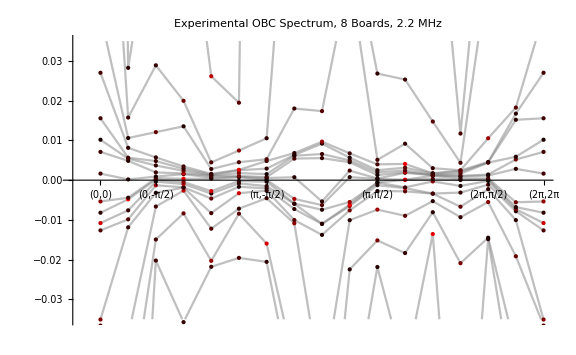
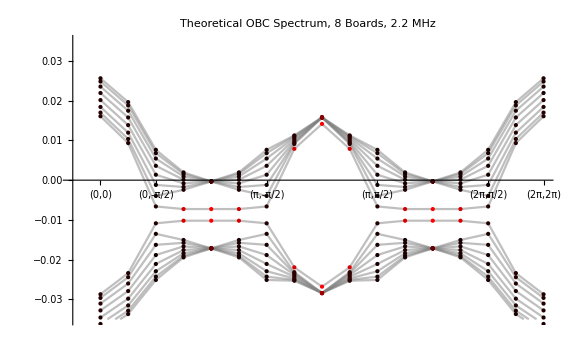
-Graphics-      (kx,ky)Laplacian Eigenvalues j_n | -Graphics-      (kx,ky)Laplacian Eigenvalues j_n
        |

-Graphics-

```mathematica
Grid[{{Labeled[Show[ListLinePlot[Transpose[experimentPath],PlotStyle->{Opacity[0.5,Gray]},Ticks->{{{1,"(0,0)"},{3,"(0,-π/2)"},{7,"(π,-π/2)"},{11,"(π,π/2)"},{15,"(2π,π/2)"},{17,"(2π,2π"}},Automatic},PlotLabel->"Experimental OBC Spectrum, "<>ToString[Nvertical]<>" Boards, "<>ToString[Frequency/(10^6)]<>" MHz",PlotRange->{-0.035,0.035},ImageSize->Large],Graphics[{PointSize[Medium],Flatten[experimentPoints,{1,2}]},Axes->True,AspectRatio->1,TicksStyle->Directive[FontOpacity->10],Ticks->{{{p1Theory,"(0,0)"},{p2Theory,"(0,π/2)"},{p3Theory,"(π,π/2)"},{p4Theory,"(π,3π/2)"},{p5Theory,"(0,3π/2)"},{p6Theory,"(0,0"}},Automatic},ImageSize->Large,PlotLabel->"Theoretical OBC Spectrum 8 Boards",PlotRange->{All,All},AxesOrigin->{0,0}]],{"      (kx,ky)","Laplacian Eigenvalues \!\(\*SubscriptBox[\(j\), \(n\)]\)"},{Bottom,Left},RotateLabel->True],Labeled[Show[ListLinePlot[Transpose[HcPathTheory],PlotStyle->{Opacity[0.5,Gray]},Ticks->{{{1,"(0,0)"},{3,"(0,-π/2)"},{7,"(π,-π/2)"},{11,"(π,π/2)"},{15,"(2π,π/2)"},{17,"(2π,2π)"}},Automatic},PlotLabel->"Theoretical OBC Spectrum, "<>ToString[Nvertical]<>" Boards, "<>ToString[Frequency/(10^6)]<>" MHz",PlotRange->{-0.035,0.035},ImageSize->Large],Graphics[{PointSize[Medium],Flatten[HcPoints,{1,2}]},Axes->True,AspectRatio->1,TicksStyle->Directive[FontOpacity->10],Ticks->{{{p1Theory,"(0,0)"},{p2Theory,"(0,π/2)"},{p3Theory,"(π,π/2)"},{p4Theory,"(π,3π/2)"},{p5Theory,"(0,3π/2)"},{p6Theory,"(0,0"}},Automatic},ImageSize->Large,PlotLabel->"OBC Spectrum 8 Boards Theory",PlotRange->{All,All},AxesOrigin->{0,0}]],{"      (kx,ky)","Laplacian Eigenvalues \!\(\*SubscriptBox[\(j\), \(n\)]\)"},{Bottom,Left},RotateLabel->True]},{"      "BarLegend[{{RGBColor[0,0,0],RGBColor[1,0,0]},{0,1}},LegendLayout->"Row",LegendLabel->"Surface Localization of Eigenvalue"],"      "BarLegend[{{RGBColor[0,0,0],RGBColor[1,0,0]},{0,1}},LegendLayout->"Row",LegendLabel->"Surface Localization of Eigenvalue"]}},Spacings->{Automatic,3},Alignment->Center]
```